```mathematica
Clear["Global`*"]
```

```mathematica
kw=10^-14;
Clear[f,g,m,n];
f[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1(10^-Pk2*c+kw))/(10^-Pk1+c))];
g[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))];
m[Pk1_,Pk2_,c_]:=-Log10[√(10^-Pk1*10^-Pk2)];
n[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1*10^-Pk2*c+10^-Pk1*kw)/c)];
(*作者给出的四个氢离子近似公式，我把它看成三元函数（k1,k2,c），再输入和输出都换成对数形式，方便后面作图*)
```

```mathematica
c=0.01;                         (*NaHA的分析浓度*)
Clear[k1,k2];
kw=10^-14;
                                             (*first一直到forth是四个图，按照从上到下的顺序*)

first=Plot3D[f[Pk1,Pk2,c],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotRange->Full,PlotStyle->Red,PlotLegends->{"PH of H_x1"},Mesh->None];

second=Plot3D[g[Pk1,Pk2,c],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"PH of H_x2"},PlotRange->Full,PlotStyle->Blue,Mesh->None];

third=Plot3D[m[Pk1,Pk2,c],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"PH of H_x3"},PlotRange->Full,PlotStyle->Purple,Mesh->None];

forth=Plot3D[n[Pk1,Pk2,c],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"PH of H_x4"},PlotRange->Full,PlotStyle->Black,Mesh->None];
```

```mathematica
(*acurate是使用精确求解方法作出的图像*)
accurate=ContourPlot3D[c+10^-PH==kw/10^-PH+c((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},PlotTheme->"Detailed",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"},PlotRange->Full]
```

-Graphics3D-

```mathematica
(*叠加*)
Show[{accurate,first}]
Show[{accurate,second}]
Show[{accurate,third}]
Show[{accurate,forth}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*此时x=-Log10[c]，便于使用manipulate交互操作，把原始方程中的c换成10^-x 即可*)
Manipulate[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme->"Scientific",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"}],{{x,0,"Pc"},-2,7}]
```

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme->"Scientific",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"}],Plot3D[f[Pk1,Pk2,10^-x],{Pk1,-10,30},{Pk2,-10,30},PlotStyle->Red,PlotLegends->{"PH of H_x1"},Mesh->None]],{{x,0,"Pc"},-2,7}]
```

Show::gcomb: Could not combine the graphics objects in Show[ContourPlot3D[10^(-FE`x$$720)+10^-PH==kw/10^Times[«2»]+(10^(-FE`x$$720) (Times[«2»]+Times[«3»]))/Plus[«3»],{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme→Scientific,ImageSize→{500,500},AxesLabel→Automatic,AxesStyle→Directive[Black,17],PlotLegends→{accurate PH}],].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme->"Scientific",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"}],Plot3D[g[Pk1,Pk2,10^-x],{Pk1,-10,30},{Pk2,-10,30},PlotStyle->Blue,PlotLegends->{"PH of H_x2"},Mesh->None]],{{x,0,"Pc"},-2,7}]
```

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme->"Scientific",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"}],Plot3D[m[Pk1,Pk2,10^-x],{Pk1,-10,30},{Pk2,-10,30},PlotStyle->Purple,PlotLegends->{"PH of H_x3"},Mesh->None]],{{x,0,"Pc"},-2,7}]
```

Show::gcomb: Could not combine the graphics objects in Show[ContourPlot3D[10^(-FE`x$$724)+10^-PH==kw/10^Times[«2»]+(10^(-FE`x$$724) (Times[«2»]+Times[«3»]))/Plus[«3»],{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme→Scientific,ImageSize→{500,500},AxesLabel→Automatic,AxesStyle→Directive[Black,17],PlotLegends→{accurate PH}],].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-10,30},{Pk2,-10,30},{PH,-2,17},PlotTheme->"Scientific",ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"accurate PH"}],Plot3D[n[Pk1,Pk2,10^-x],{Pk1,-10,30},{Pk2,-10,30},PlotStyle->Black,PlotLegends->{"PH of H_x4"},Mesh->None]],{{x,0,"Pc"},-2,7}]
```

```mathematica
Show[accurate,third]
```

-Graphics3D-

```mathematica
Show[accurate]
```

-Graphics3D-

```mathematica
(*刻画误差*)
c=0.01;
sup=ContourPlot3D[c+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+c((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},ContourStyle->Green,ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"sup"},PlotRange->Full,PlotTheme->"Scientific"];
inf=ContourPlot3D[c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},ContourStyle->Yellow,ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"inf"},PlotRange->Full,PlotTheme->"Scientific"];
(*酸性物质和碱性物质、实际情况*)
acidbase=ContourPlot3D[x+y==14,{x,-20,20},{y,-20,20},{z,-5,14},Mesh->None,ContourStyle->{RGBColor[0.8, 0.55, 0.15],Opacity[0.3]},PlotLegends->{"boundary between acid-substance and base-substance"},PlotTheme->"Scientific"];
reality=ContourPlot3D[x==y,{x,-20,20},{y,-20,20},{z,-5,14},Mesh->None,ContourStyle->{Opacity[0.3],RGBColor[0.09343302790162711, 0.6244081234960046, 0.8545690421483247],Specularity[White,50]},PlotLegends->{"in reality"},PlotTheme->"Scientific"];
```

```mathematica
Show[sup,inf,third]
Show[sup,third]
Show[inf,third]
Show[acidbase,reality]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*制定计算方案*)
Manipulate[Show[ContourPlot3D[x==a,{x,0,20},{y,0,20},{z,0,14},Mesh->None,ContourStyle->{Opacity[0.3],Specularity[White,50]},PlotLegends->{"constant Pk1"},PlotTheme->"Scientific"],ContourPlot3D[y==b,{x,0,20},{y,0,20},{z,0,14},Mesh->None,ContourStyle->{Opacity[0.3],Specularity[White,50]},PlotLegends->{"constant Pk2"},PlotTheme->"Scientific"],ContourPlot3D[z==c,{x,0,20},{y,0,20},{z,0,14},Mesh->None,ContourStyle->{Opacity[0.3],Specularity[White,50]},PlotLegends->{"constant PH"},PlotTheme->"Scientific"]],{{a,10},0,20},{{b,10},0,20},{{c,5},0,14}]
Show[sup,third,ContourPlot3D[x==5,{x,0,20},{y,0,20},{z,0,14},Mesh->None,ContourStyle->{Opacity[0.3],Specularity[White,50]},PlotLegends->{"constant Pk1"},PlotTheme->"Scientific"]]
```

-Graphics3D-

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

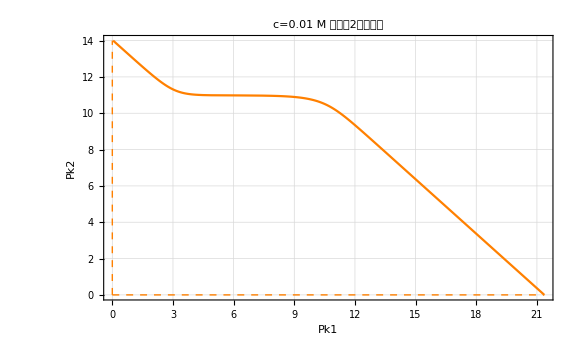

```mathematica
(*制定计算方案*)
c=0.01;
cp3sup=Table[{FindRoot[{c+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+c((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.01}];
cp3supline=ListLinePlot[cp3sup,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[c=0.01M 时公式2的可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large];

Show[cp3supline,Graphics[{Thick,Dashed,Orange,Line[{{0,0},{0,14}}]}],Graphics[{Thick,Dashed,Orange,Line[{{0,0},cp3sup[[1]]}]}]]
```

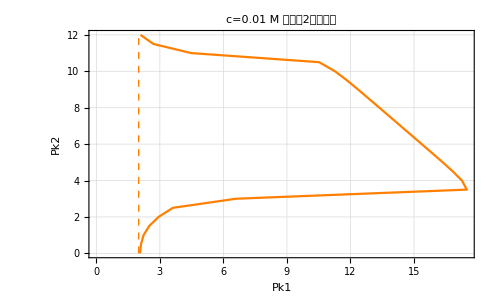

```mathematica
(*优化算法之前*)
goodarea2=ListLinePlot[criticalpoints2,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[c=0.01M 时公式2的可行域],LabelStyle->{GrayLevel[0]}];

Show[goodarea2,Graphics[{Thick,Dashed,Orange,Line[{{2,0},{2,12}}]}]]
```

```mathematica
Show[inf,third]
```

-Graphics3D-

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

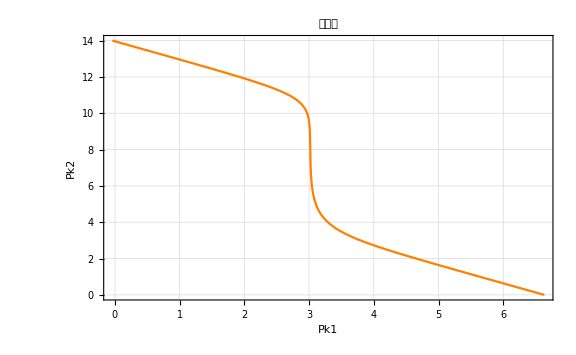

```mathematica
(*同理*)
cp3inf=Table[{FindRoot[{c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.01}];
cp3infline=ListLinePlot[cp3inf,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large];
Show[cp3infline]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

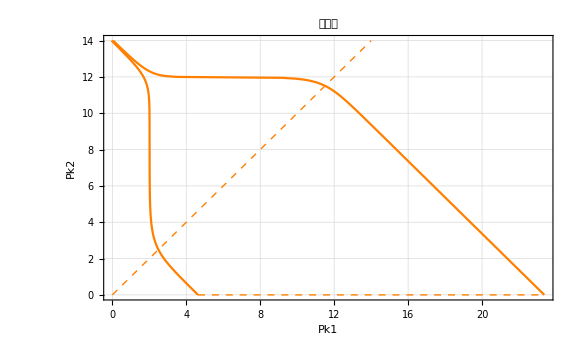

```mathematica
(*整合*)
c=0.1;
cp3sup=Table[{FindRoot[{c+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+c((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.05}];
cp3supline=ListLinePlot[cp3sup,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large];

cp3inf=Table[{FindRoot[{c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.05}];
cp3infline=ListLinePlot[cp3inf,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large];

Show[cp3supline,cp3infline,Graphics[{Thick,Dashed,Orange,Line[{cp3inf[[1]],cp3sup[[1]]}]}],Graphics[{Thick,Dashed,Orange,Line[{{0,0},{14,14}}]}]]
```

```mathematica
Clear[c];
Manipulate[Show[ListLinePlot[Table[{FindRoot[{10^-Pc+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+10^-Pc*((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.05}],PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large],ListLinePlot[Table[{FindRoot[{10^-Pc+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+10^-Pc*((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==1/2 Pk1+1/2 Pk2,Pk2==a},{Pk1,20},{Pk2,a},{PH,20},WorkingPrecision->MachinePrecision][[1,2]],a},{a,0,14,0.05}],PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[可行域],LabelStyle->{15,GrayLevel[0]},ImageSize->Large],Graphics[{Thick,Dashed,Orange,Line[{cp3inf[[1]],cp3sup[[1]]}]}],Graphics[{Thick,Dashed,Orange,Line[{{0,0},{14,14}}]}]],{{Pc,"Pc"},-2,7}]
```

FindRoot::nlnum: The function value {-2.5704-9.54993×10^19 kw,10.,0.} is not a list of numbers with dimensions {3} at {Pk1,Pk2,PH} = {20.,0.,20.}.

FindRoot::nlnum: The function value {-2.5704-9.54993×10^19 kw,9.975,0.} is not a list of numbers with dimensions {3} at {Pk1,Pk2,PH} = {20.,0.05,20.}.

FindRoot::nlnum: The function value {-2.5704-9.54993×10^19 kw,9.95,0.} is not a list of numbers with dimensions {3} at {Pk1,Pk2,PH} = {20.,0.1,20.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partd: Part specification cp3inf⟦1⟧ is longer than depth of object.

Part::partd: Part specification cp3sup⟦1⟧ is longer than depth of object.

```mathematica
(*上三维图*)
cp3infsurface=ContourPlot3D[10^-Pc+10^(-(1/2 Pk1+1/2 Pk2+0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{RGBColor[0.5355579515419151, 0.9430131641554946, 0.004882822085237493],Opacity[0.5]},ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"surface for inf"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None];
cp3supsurface=ContourPlot3D[10^-Pc+10^(-(1/2 Pk1+1/2 Pk2-0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{RGBColor[0.5864078175768783, 0.26359194937432395, 0.519486597936422],Opacity[0.5]},ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"surface for sup"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None];
shadow3inf=Plot3D[-Log10[(kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))-10^(-(1/2 Pk1+1/2 Pk2+0.02)))/(1-((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)))],{Pk1,-1,20},{Pk2,-5,16},PlotStyle->Directive[RGBColor[0.5355579515419151, 0.9430131641554946, 0.004882822085237493],Opacity[0]],Filling->Bottom,Mesh->None,BoundaryStyle->None];
shadow3sup=Plot3D[-Log10[(kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))-10^(-(1/2 Pk1+1/2 Pk2-0.02)))/(1-((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)))],{Pk1,-1,20},{Pk2,-5,16},PlotStyle->Directive[RGBColor[0.5864078175768783, 0.26359194937432395, 0.519486597936422],Opacity[0]],Filling->Bottom,Mesh->None,BoundaryStyle->None];
Show[cp3infsurface,cp3supsurface,shadow3inf,shadow3sup]
```

-Graphics3D-

```mathematica
cp3infsurfacefull=ContourPlot3D[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2+0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2+0.0043)==kw/10^-(1/2 Pk1+1/2 Pk2+0.0043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2+0.0043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2+0.0043))+10^-(1/2 Pk1+1/2 Pk2+0.0043)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2+0.000434)==kw/10^-(1/2 Pk1+1/2 Pk2+0.000434)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2+0.000434)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2+0.000434))+10^-(1/2 Pk1+1/2 Pk2+0.000434)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2+0.000043)==kw/10^-(1/2 Pk1+1/2 Pk2+0.000043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2+0.000043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2+0.000043))+10^-(1/2 Pk1+1/2 Pk2+0.000043)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2+0.0000043)==kw/10^-(1/2 Pk1+1/2 Pk2+0.0000043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2+0.0000043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2+0.0000043))+10^-(1/2 Pk1+1/2 Pk2+0.0000043)*10^-Pk1+10^-Pk1*10^-Pk2))},{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{Opacity[0.25]},ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotLegends->{"-5%","-1%","-0.1%","-0.01%","-0.001%"},PlotRange->Full,PlotTheme->"Detailed",Mesh->None]
```

-Graphics3D-

```mathematica
cp3supsurfacefull=cp3supsurface=ContourPlot3D[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2-0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2-0.0043)==kw/10^-(1/2 Pk1+1/2 Pk2-0.0043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2-0.0043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2-0.0043))+10^-(1/2 Pk1+1/2 Pk2-0.0043)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2-0.00043)==kw/10^-(1/2 Pk1+1/2 Pk2-0.00043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2-0.00043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2-0.00043))+10^-(1/2 Pk1+1/2 Pk2-0.00043)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2-0.000043)==kw/10^-(1/2 Pk1+1/2 Pk2-0.000043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2-0.000043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2-0.000043))+10^-(1/2 Pk1+1/2 Pk2-0.000043)*10^-Pk1+10^-Pk1*10^-Pk2)),10^-Pc+10^-(1/2 Pk1+1/2 Pk2-0.0000043)==kw/10^-(1/2 Pk1+1/2 Pk2-0.0000043)+10^-Pc*((10^-(1/2 Pk1+1/2 Pk2-0.0000043)*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2 (1/2 Pk1+1/2 Pk2-0.0000043))+10^-(1/2 Pk1+1/2 Pk2-0.0000043)*10^-Pk1+10^-Pk1*10^-Pk2))},{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{Opacity[0.25]},ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotRange->Full,PlotTheme->"Detailed",PlotLegends->{"5%","1%","0.1%","0.01%","0.001%"},Mesh->None]
```

-Graphics3D-

```mathematica
frame=ContourPlot3D[Pc==-10,{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ImageSize->{500,500},AxesLabel->Automatic,AxesStyle->Directive[Black, 17],PlotRange->Full,PlotTheme->"Scientific",Mesh->None,PlotLabel->"不同误差对应的可行域边界"];
Show[frame,cp3infsurfacefull,cp3supsurfacefull]
Export["/Users/royalty/Desktop/Chemistry courses/analytical/不同误差对应的可行域边界.png",Show[frame,cp3infsurfacefull,cp3supsurfacefull]]
```

-Graphics3D-

/Users/royalty/Desktop/Chemistry courses/analytical/不同误差对应的可行域边界.png

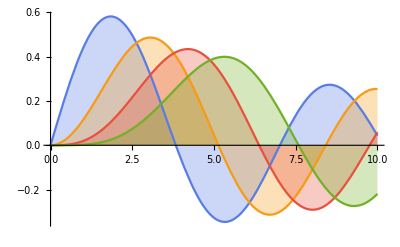

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,PlotTheme->"BoldColor",PlotTheme->"Scientific"]
```

```mathematica
Log10[1.0001]
```

0.0000434273

```mathematica
(*总结所有的浓度情况，Manipulate*)
Manipulate[Show[cp3infsurface,cp3supsurface,shadow3inf,shadow3sup,ContourPlot3D[z==Pc,{x,-1,20},{y,-5,16},{z,-1,7},Mesh->None,ContourStyle->{Opacity[0.9]}]],{{Pc,3,"Pc"},-1,7}]
```

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
(*讨论三个条件*)condition1=ContourPlot3D[Pc-Pk2==-Log10[120],{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},Mesh->None,PlotLegends->{"condition 1"},PlotTheme->"Scientific",ContourStyle->{Opacity[0.9],RGBColor[0.9237197992436841, 0.6219223959579392, 0.1650285445112396]}];
condition2=ContourPlot3D[Pc-Pk1==-Log10[20],{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},Mesh->None,PlotLegends->{"condition 2"},PlotTheme->"Scientific",ContourStyle->{Opacity[0.9],RGBColor[0.26352949004736725, 0.31733146118166156, 0.579684358633165]}];
condition3=ContourPlot3D[Pc+Pk2==-Log10[20*kw],{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},Mesh->None,PlotLegends->{"condition 3"},PlotTheme->"Scientific",ContourStyle->{Opacity[0.9],RGBColor[0.07161690378467722, 0.5233977415051496, 0.7847091614018282]}];
Show[cp3infsurface,cp3supsurface,shadow3inf,shadow3sup,condition1]
Show[cp3infsurface,cp3supsurface,shadow3inf,shadow3sup,condition2,condition3]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*完善适用条件*)
xoy=ContourPlot3D[z==0,{x,-1,20},{y,-5,16},{z,-1,7},ContourStyle->{RGBColor[0.7253178029248672, 0.04367428090598513, 0.746808477598091],Opacity[0.4]},Mesh->None,AxesLabel->Automatic,AxesStyle->Directive[Black, 14]];
Show[cp3supsurface,xoy]
```

-Graphics3D-

```mathematica
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2+0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pc==0,Pk2==0},{Pc,Pk1,Pk2},Reals]
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2+0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pc==6,Pk1==14},{Pc,Pk1,Pk2},Reals]
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2+0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2+0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2+0.02))+10^(-(1/2 Pk1+1/2 Pk2+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pc==0,Pk1==1.5},{Pc,Pk1,Pk2},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→0,Pk1→2.65431,Pk2→0}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→6.,Pk1→14.,Pk2→-0.238136}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→0,Pk1→1.5,Pk2→1.47909}}

```mathematica
NSolve[{2.65431/a==1,14/a+-0.238/b+6/c==1,1.5/a+1.479/b==1},{a,b,c},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→2.65431,b→3.40093,c→-1.42706}}

```mathematica
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2-0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pc==0,Pk1==20},{Pc,Pk1,Pk2},Reals]
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2-0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pc==0,Pk1==12},{Pc,Pk1,Pk2},Reals]
Solve[{10^-Pc+10^(-(1/2 Pk1+1/2 Pk2-0.02))==kw/10^(-(1/2 Pk1+1/2 Pk2-0.02))+10^-Pc*((10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(1/2 Pk1+1/2 Pk2-0.02))+10^(-(1/2 Pk1+1/2 Pk2-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),Pk2==-5,Pk1==20},{Pc,Pk1,Pk2},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→0,Pk1→20.,Pk2→5.36588}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→0,Pk1→12.,Pk2→12.7091}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pc→5.23338,Pk1→20.,Pk2→-5.}}

```mathematica
Solve[{20/a+5.36/b==1,12/a+12.7/b==1,20/a+-5/b+5.23/c==1},{a,b,c},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→25.842,b→23.71,c→11.9694}}

```mathematica
approximation3inf=ContourPlot3D[x/2.65431+y/3.40093+z/-1.42706==1,{x,-5,20},{y,-5,16},{z,-1,7},PlotTheme->"Scientific",ImageSize->{500,500},Mesh->None,AxesLabel->Automatic,AxesStyle->Directive[Black, 17],ContourStyle->{RGBColor[0.5355579515419151, 0.9430131641554946, 0.004882822085237493],Opacity[0.5]},PlotLegends->{"approximation for inf"}];
approximation3sup=ContourPlot3D[x/26+y/24+z/12==1,{x,-5,20},{y,-5,16},{z,-1,7},PlotTheme->"Scientific",ImageSize->{500,500},Mesh->None,AxesLabel->Automatic,AxesStyle->Directive[Black, 17],ContourStyle->{RGBColor[0.5864078175768783, 0.26359194937432395, 0.519486597936422],Opacity[0.5]},PlotLegends->{"approximation for sup"}];Show[condition2,condition3]
Show[approximation3sup,approximation3inf,condition2,condition3]
```

-Graphics3D-

-Graphics3D-

```mathematica
Pc ≤ -1.42706*(1-Pk1/2.65431-Pk2/3.40093)
Pc ≤ 12*(1-Pk1/26-Pk2/24)
Pc-Pk1<-Log10[20]
Pc+Pk2<-Log10[20*Kw]
```

```mathematica
NSolve[{Pc==-1,Pk1==0,10^-Pc+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))==kw/(10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02)))+10^-Pc*((10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+10^-Pk1*10^-Pk2))},{Pc,Pk1,Pk2},Reals]
NSolve[{Pc+Pk2==-Log10[x]-Log10[kw],Pc==-1,Pk2==13.984429177784698},{Pc,Pk2,x},Reals]
```

{{Pc→-1.,Pk1→0,Pk2→13.9844}}

{{Pc→-1.,Pk2→13.9844,x→10.365}}

```mathematica
Show[cp3infsurface,cp3supsurface,ContourPlot3D[Pc+Pk2==-Log10[10.365036176244413]-Log10[kw],{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7}]]
```

-Graphics3D-

```mathematica
10.365036176244413
```